```mathematica
(* This function calculates QFIM of density matrix "mat" for variables "variables" *)
Fisher[mat_,variables_]:=(
result=Array[0&,{Length[variables],Length[variables]}];
evals=Simplify[Eigenvalues[mat]];
evecs=Eigenvectors[mat];
For[i=1,i≤Length[variables],i++,
For[j=1,j≤Length[variables],j++,
firstVar=variables[[i]];
secondVar=variables[[j]];
fisher1=fisher2=fisher3=0;
For[k=1,k≤Length[evals],k++,
If[evals[[k]]=!=0,
eval1=evals[[k]];
evec1=evecs[[k]];
KetEvec1=Simplify[Transpose[{evec1}]];
BraEvec1=Simplify[ConjugateTranspose[KetEvec1]];
norm1=Sqrt[(Simplify[BraEvec1.KetEvec1])[[1,1]]];
KetEvec1=Simplify[KetEvec1/norm1];
BraEvec1=Simplify[BraEvec1/norm1];
BraEvec1Prime1=D[BraEvec1,firstVar];
KetEvec1Prime1=D[KetEvec1,firstVar];
BraEvec1Prime2=D[BraEvec1,secondVar];
KetEvec1Prime2=D[KetEvec1,secondVar];

eval1Prime1=D[eval1,firstVar];
eval1Prime2=D[eval1,secondVar];

fisher1+=eval1Prime1*eval1Prime2/eval1;
fisher2+=eval1*Re[(BraEvec1Prime1.KetEvec1Prime2)[[1,1]]];
For[l=1,l≤Length[evals],l++,
If[evals[[l]]=!=0 ,
eval2=evals[[l]];
evec2=evecs[[l]];
KetEvec2=Simplify[Transpose[{evec2}]];
BraEvec2=Simplify[ConjugateTranspose[KetEvec2]];
norm2=Sqrt[(Simplify[BraEvec2.KetEvec2])[[1,1]]];
KetEvec2=Simplify[KetEvec2/norm2];
BraEvec2=Simplify[BraEvec2/norm2];
BraEvec2Prime1=D[BraEvec2,firstVar];
KetEvec2Prime1=D[KetEvec2,firstVar];
BraEvec2Prime2=D[BraEvec2,secondVar];
KetEvec2Prime2=D[KetEvec2,secondVar];
fisher3+=eval1*eval2*Re[(BraEvec1Prime1.KetEvec2)[[1,1]] *(BraEvec2.KetEvec1Prime2 )[[1,1]]]/(eval1+eval2);
];
];
];
];
Print[variables[[i]],variables[[j]]," done"];
result[[i,j]]=(fisher1+4*fisher2-8*fisher3)//Simplify;
];
];
ClearAll[i,j,k,l,fisher1,fisher2,fisher3,KetEvec1,KetEvec1Prime1,KetEvec1Prime2,KetEvec2,KetEvec2Prime1,KetEvec2Prime2,BraEvec1,BraEvec1Prime1,BraEvec1Prime2,BraEvec2,BraEvec2Prime1,BraEvec2Prime2,evecs,evec1,evec2,evals,eval1,eval1Prime1,eval2,eval1Prime2,firstVar,secondVar];
Return[result];
);
```

```mathematica
(* three Photons in mach zehnder - there are 10 distinct states *)
(* set global assumptions *)
$Assumptions={T,ϕ,γ}∈Reals&&T>=0&&T<=1; 
(* Define transmission and reflection coefficients *)
t=T Exp[-I γ];
r=Sqrt[1-T^2];
(*  |ψ> =[|300>,|210>,|120>,|030>,|201>,|111>,|021>,|102>,|012>,|003>]  *)
a1=-I/8(t- Exp[-I ϕ])^3;
a2=Sqrt[3]/8( t-Exp[-I ϕ])(t^2 -Exp[-2I ϕ]);
a3=I Sqrt[3]/8(t+ Exp[-I ϕ])(t^2- Exp[-2I ϕ]);
a4=-1/8(t+ Exp[-I ϕ])^3;
a5=-I Sqrt[3/8]r/2(t- Exp[-I ϕ])^2;
a6=Sqrt[3/16]r(t^2- Exp[-2I ϕ]);
a7=I Sqrt[3/8]r/2(t+ Exp[-I ϕ])^2;
a8=-I Sqrt[3/16]r^2(t- Exp[-I ϕ]);
a9=Sqrt[3/16]r^2(t+ Exp[-I ϕ]);
a10=-I r^3/Sqrt[8];

ψ={{a1},{a2},{a3},{a4},{a5},{a6},{a7},{a8},{a9},{a10}};
ψ//MatrixForm
ρ=ψ.ConjugateTranspose[ψ]//Simplify;
Norm[ψ]//FullSimplify
```

(-1/8 ⅈ (-ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T)^3
1/8 √3 (-ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T) (-ⅇ^(-2 ⅈ ϕ)+ⅇ^(-2 ⅈ γ) T^2)
1/8 ⅈ √3 (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T) (-ⅇ^(-2 ⅈ ϕ)+ⅇ^(-2 ⅈ γ) T^2)
-1/8 (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T)^3
-1/4 ⅈ √(3/2) (-ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T)^2 √(1-T^2)
1/4 √3 √(1-T^2) (-ⅇ^(-2 ⅈ ϕ)+ⅇ^(-2 ⅈ γ) T^2)
1/4 ⅈ √(3/2) (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T)^2 √(1-T^2)
-1/4 ⅈ √3 (-ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T) (1-T^2)
1/4 √3 (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T) (1-T^2)
-(ⅈ (1-T^2)^(3/2))/(2 √2))

1

```mathematica
(* Tracing over dissipated photons in path |w> *)
For[i=1,i≤4,i++,
For[j=5,j≤10,j++,
ρ[[i,j]]=ρ[[j,i]]=0;
];
];
For[i=5,i≤7,i++,
For[j=8,j≤10,j++,
ρ[[i,j]]=ρ[[j,i]]=0;
];
];
For[i=8,i≤9,i++,
ρ[[i,10]]=ρ[[10,i]]=0;
];
ρ//MatrixForm
```

(1/64 (1-ⅇ^(-ⅈ (γ-ϕ)) T-ⅇ^(ⅈ (γ-ϕ)) T+T^2)^3 | 1/64 ⅈ √3 ⅇ^(-3 ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)-ⅇ^(ⅈ γ) T)^2 (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ ϕ) T)^3 | -1/64 √3 (-ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T)^3 (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T) (-ⅇ^(2 ⅈ ϕ)+ⅇ^(2 ⅈ γ) T^2) | 1/64 ⅈ (-ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T)^3 (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T)^3 | 0 | 0 | 0 | 0 | 0 | 0
1/64 ⅈ √3 ⅇ^(-3 ⅈ (γ+ϕ)) (-ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T)^3 (ⅇ^(ⅈ γ)-ⅇ^(ⅈ ϕ) T)^2 (ⅇ^(ⅈ γ)+ⅇ^(ⅈ ϕ) T) | 3/64 ⅇ^(-3 ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)-ⅇ^(ⅈ γ) T)^2 (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ ϕ) T)^2 (ⅇ^(ⅈ γ)+ⅇ^(ⅈ ϕ) T) | 3/64 ⅈ ⅇ^(-3 ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)-ⅇ^(ⅈ γ) T) (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T)^2 (ⅇ^(ⅈ γ)-ⅇ^(ⅈ ϕ) T)^2 (ⅇ^(ⅈ γ)+ⅇ^(ⅈ ϕ) T) | -1/64 √3 ⅇ^(-3 ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T)^3 (ⅇ^(ⅈ γ)-ⅇ^(ⅈ ϕ) T)^2 (ⅇ^(ⅈ γ)+ⅇ^(ⅈ ϕ) T) | 0 | 0 | 0 | 0 | 0 | 0
-1/64 √3 (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T) (-ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T)^3 (-ⅇ^(-2 ⅈ ϕ)+ⅇ^(-2 ⅈ γ) T^2) | -3/64 ⅈ ⅇ^(-3 ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)-ⅇ^(ⅈ γ) T)^2 (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ ϕ) T) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ ϕ) T)^2 | 3/64 ⅇ^(-3 ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)-ⅇ^(ⅈ γ) T) (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T)^2 (ⅇ^(ⅈ γ)-ⅇ^(ⅈ ϕ) T) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ ϕ) T)^2 | -1/64 ⅈ √3 (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T) (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T)^3 (-ⅇ^(-2 ⅈ ϕ)+ⅇ^(-2 ⅈ γ) T^2) | 0 | 0 | 0 | 0 | 0 | 0
-1/64 ⅈ (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T)^3 (-ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T)^3 | -1/64 √3 ⅇ^(-3 ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)-ⅇ^(ⅈ γ) T)^2 (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ ϕ) T)^3 | 1/64 ⅈ √3 (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T)^3 (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T) (-ⅇ^(2 ⅈ ϕ)+ⅇ^(2 ⅈ γ) T^2) | 1/64 (ⅇ^(-ⅈ ϕ)+ⅇ^(-ⅈ γ) T)^3 (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T)^3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -3/32 ⅇ^(-2 ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)-ⅇ^(ⅈ γ) T)^2 (ⅇ^(ⅈ γ)-ⅇ^(ⅈ ϕ) T)^2 (-1+T^2) | (3 ⅈ ⅇ^(-2 ⅈ (γ+ϕ)) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ ϕ) T)^2 (-1+T^2) (-ⅇ^(2 ⅈ ϕ)+ⅇ^(2 ⅈ γ) T^2))/(16 √2) | 3/32 ⅇ^(-2 ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T)^2 (ⅇ^(ⅈ γ)-ⅇ^(ⅈ ϕ) T)^2 (-1+T^2) | 0 | 0 | 0
0 | 0 | 0 | 0 | -(3 ⅈ ⅇ^(-2 ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)-ⅇ^(ⅈ γ) T)^2 (-1+T^2) (-ⅇ^(2 ⅈ γ)+ⅇ^(2 ⅈ ϕ) T^2))/(16 √2) | 3/16 ⅇ^(-2 ⅈ (γ+ϕ)) (-1+T^2) (ⅇ^(2 ⅈ ϕ)-ⅇ^(2 ⅈ γ) T^2) (-ⅇ^(2 ⅈ γ)+ⅇ^(2 ⅈ ϕ) T^2) | (3 ⅈ ⅇ^(-2 ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T)^2 (-1+T^2) (-ⅇ^(2 ⅈ γ)+ⅇ^(2 ⅈ ϕ) T^2))/(16 √2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 3/32 ⅇ^(-2 ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)-ⅇ^(ⅈ γ) T)^2 (ⅇ^(ⅈ γ)+ⅇ^(ⅈ ϕ) T)^2 (-1+T^2) | (3 ⅈ ⅇ^(-2 ⅈ (γ+ϕ)) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ ϕ) T)^2 (-1+T^2) (ⅇ^(2 ⅈ ϕ)-ⅇ^(2 ⅈ γ) T^2))/(16 √2) | -3/32 ⅇ^(-2 ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T)^2 (ⅇ^(ⅈ γ)+ⅇ^(ⅈ ϕ) T)^2 (-1+T^2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/16 ⅇ^(-ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)-ⅇ^(ⅈ γ) T) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ ϕ) T) (-1+T^2)^2 | 3/16 ⅈ ⅇ^(-ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T) (ⅇ^(ⅈ γ)-ⅇ^(ⅈ ϕ) T) (-1+T^2)^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3/16 ⅈ ⅇ^(-ⅈ (γ+ϕ)) (-ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ ϕ) T) (-1+T^2)^2 | 3/16 ⅇ^(-ⅈ (γ+ϕ)) (ⅇ^(ⅈ ϕ)+ⅇ^(ⅈ γ) T) (ⅇ^(ⅈ γ)+ⅇ^(ⅈ ϕ) T) (-1+T^2)^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/8 (-1+T^2)^3)

```mathematica
(* Calculate Quantum Fisher Information Matrix *)
fisher=Fisher[ρ,{ϕ,γ,T}];
```

ϕϕ done

ϕγ done

ϕT done

γϕ done

γγ done

γT done

Tϕ done

Tγ done

TT done

```mathematica
(* Simplify eqautions obtained for QFIM *)
fisher=fisher//ComplexExpand//Simplify;
fisher//MatrixForm
```

((6 T^2)/(1+T^2) | -(6 T^2)/(1+T^2) | 0
-(6 T^2)/(1+T^2) | (6 T^2)/(1+T^2) | 0
0 | 0 | -6/(-1+T^2))

```mathematica
(* Calulate determinant of QFIM *)
Det[fisher]//Simplify
```

0

```mathematica
(* Calculate variance and covariance for objects characteristics *)
reducedfisher={{fisher[[2,2]],fisher[[2,3]]},{fisher[[3,2]],fisher[[3,3]]}};
cov=Inverse[reducedfisher]//Simplify;
cov//MatrixForm
```

(1/6 (1+1/T^2) | 0
0 | 1/6 (1-T^2))

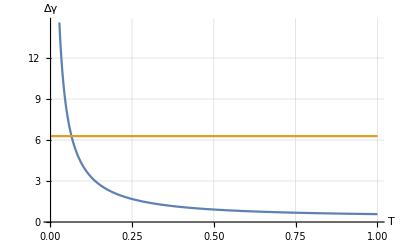

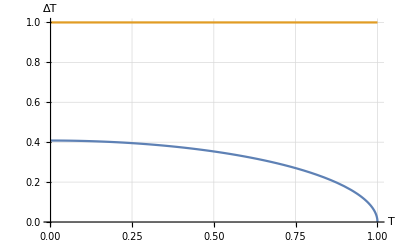

{28.2843 √((0.9696+15.2379 Re[1/1]+6)/1),14.1421 √(1/1),5.65685 √((30.+7)/1),2 √(1/Re[(6+12 ⅇ^1)/(1)^2])}
 |  |  |  |

```mathematica
p1=Plot[{Sqrt[cov[[1,1]]],2*Pi},{T,0.001,1},AxesLabel->{"T","Δγ"},GridLines->Automatic]
p2=Plot[{Sqrt[cov[[2,2]]],1},{T,0.001,1},AxesLabel->{"T","ΔT"},GridLines->Automatic]
Export["three-photon-dg.png",p1,ImageResolution->300];
Export["three-photon-dt.png",p2,ImageResolution->300];
```

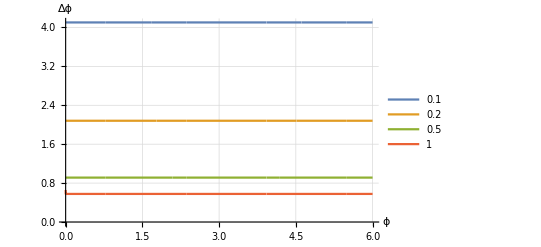

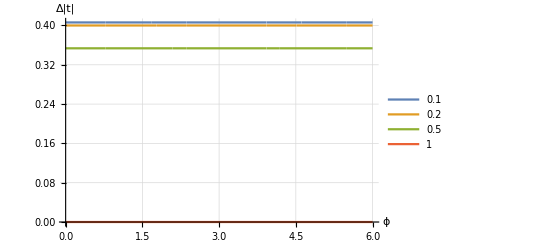

```mathematica
xx=Table[Sqrt[b[[1,1]]],{t,{0.1,0.2,0.5,1}}];
yy=Table[Sqrt[b[[2,2]]],{t,{0.1,0.2,0.5,1}}];
p1=Plot[xx,{ϕ,0,6},AxesLabel->{"ϕ","Δϕ"},GridLines->Automatic, PlotLegends->{0.1,0.2,0.5,1}]
p2=Plot[yy,{ϕ,0,6},AxesLabel->{"ϕ","Δ|t|"},GridLines->Automatic,PlotLegends->{0.1,0.2,0.5,1}]
```